```mathematica
Ψ[r,θ]=∑_(l=0)^∞ (Subscript[A, l] r^l+Subscript[B, l]/r^(l+1))LegendreP[l,u=Cos[θ]]
```

```mathematica
MatrixForm[Table[{Rr^l LegendreP[l,Cos[Ttheta]],1/Rr^(l+1)LegendreP[l,Cos[Ttheta]]},{l,0,7}]]
```

(1 | 1/Rr
Rr Cos[Ttheta] | Cos[Ttheta]/Rr^2
1/2 Rr^2 (-1+3 Cos[Ttheta]^2) | (-1+3 Cos[Ttheta]^2)/(2 Rr^3)
1/2 Rr^3 (-3 Cos[Ttheta]+5 Cos[Ttheta]^3) | (-3 Cos[Ttheta]+5 Cos[Ttheta]^3)/(2 Rr^4)
1/8 Rr^4 (3-30 Cos[Ttheta]^2+35 Cos[Ttheta]^4) | (3-30 Cos[Ttheta]^2+35 Cos[Ttheta]^4)/(8 Rr^5)
1/8 Rr^5 (15 Cos[Ttheta]-70 Cos[Ttheta]^3+63 Cos[Ttheta]^5) | (15 Cos[Ttheta]-70 Cos[Ttheta]^3+63 Cos[Ttheta]^5)/(8 Rr^6)
1/16 Rr^6 (-5+105 Cos[Ttheta]^2-315 Cos[Ttheta]^4+231 Cos[Ttheta]^6) | (-5+105 Cos[Ttheta]^2-315 Cos[Ttheta]^4+231 Cos[Ttheta]^6)/(16 Rr^7)
1/16 Rr^7 (-35 Cos[Ttheta]+315 Cos[Ttheta]^3-693 Cos[Ttheta]^5+429 Cos[Ttheta]^7) | (-35 Cos[Ttheta]+315 Cos[Ttheta]^3-693 Cos[Ttheta]^5+429 Cos[Ttheta]^7)/(16 Rr^8))

```mathematica
Needs["VectorAnalysis`"]
```

```mathematica
Needs["VectorFieldPlots`"]
```

```mathematica
Coordinates[Spherical]
```

{Rr,Ttheta,Pphi}

```mathematica
******************* //1
```

```mathematica
Laplacian[A]
```

```mathematica
0 // no field, so A can be set arbitary
```

```mathematica
******************* // 1/Rr
```

```mathematica
Grad[1/Rr,Spherical]
```

{-1/Rr^2,0,0}

```mathematica
Div[{-1/Rr^2,0,0},Spherical]
```

0

```mathematica
******************* // Cos[Ttheta]Rr
```

```mathematica
Grad[Cos[Ttheta]Rr,Spherical]
```

```mathematica
{Cos[θ],-Sin[θ],0}/.{Cos[θ]->z/(√(x^2+y^2+z^2)),Sin[θ]->(√(x^2+y^2))/(√(x^2+y^2+z^2)),Sin[ϕ]->y/(√(x^2+y^2)),Cos[ϕ]->x/(√(x^2+y^2))}
```

```mathematica
{z/(√(x^2+y^2+z^2)),-(√(x^2+y^2))/(√(x^2+y^2+z^2)),0}
```

```mathematica
MatrixForm[TT]
```

(x/(√(x^2+y^2+z^2)) | (x z)/(√(x^2+y^2) √(x^2+y^2+z^2)) | -y/(√(x^2+y^2))
y/(√(x^2+y^2+z^2)) | (y z)/(√(x^2+y^2) √(x^2+y^2+z^2)) | x/(√(x^2+y^2))
z/(√(x^2+y^2+z^2)) | -(√(x^2+y^2))/(√(x^2+y^2+z^2)) | 0)

```mathematica
Simplify[TT.{z/(√(x^2+y^2+z^2)),-(√(x^2+y^2))/(√(x^2+y^2+z^2)),0}]
```

{0,0,1}

```mathematica
Laplacian[Cos[Ttheta]Rr,Spherical]
```

0

```mathematica
or//
```

```mathematica
Cos[Ttheta]Rr/.{Cos[Ttheta]->Zz/(√(Xx^2+Yy^2+Zz^2)),Sin[Ttheta]->(√(Xx^2+Yy^2))/(√(Xx^2+Yy^2+Zz^2)),Sin[Pphi]->Yy/(√(Xx^2+Yy^2)),Cos[Pphi]->Xx/(√(Xx^2+Yy^2)),Rr->√(Xx^2+Yy^2+Zz^2)}
```

Zz

```mathematica
Grad[Zz,Cartesian]
```

{0,0,1}

```mathematica
*************************************  Cos[Ttheta] 1/Rr^2
```

```mathematica
FullSimplify[Grad[Cos[Ttheta] 1/Rr^2,Spherical]]
```

{-(2 Cos[Ttheta])/Rr^3,-Sin[Ttheta]/Rr^3,0}

```mathematica
Laplacian[Cos[Ttheta] 1/Rr^2,Spherical]
```

0

```mathematica
Simplify[Cos[Ttheta] 1/Rr^2/.{Cos[Ttheta]->Zz/(√(Xx^2+Yy^2+Zz^2)),Sin[Ttheta]->(√(Xx^2+Yy^2))/(√(Xx^2+Yy^2+Zz^2)),Sin[Pphi]->Yy/(√(Xx^2+Yy^2)),Cos[Pphi]->Xx/(√(Xx^2+Yy^2)),Rr->√(Xx^2+Yy^2+Zz^2)}]
```

Zz/((Xx^2+Yy^2+Zz^2)^(3/2))

```mathematica
Simplify[Grad[Zz/((Xx^2+Yy^2+Zz^2)^(3/2))]]
```

```mathematica
{-(3 Xx Zz)/((Xx^2+Yy^2+Zz^2)^(5/2)),-(3 Yy Zz)/((Xx^2+Yy^2+Zz^2)^(5/2)),(Xx^2+Yy^2-2 Zz^2)/((Xx^2+Yy^2+Zz^2)^(5/2))}/.{Xx->x,Yy->y,Zz->z}
```

{-(3 x z)/((x^2+y^2+z^2)^(5/2)),-(3 y z)/((x^2+y^2+z^2)^(5/2)),(x^2+y^2-2 z^2)/((x^2+y^2+z^2)^(5/2))}

```mathematica
Manipulate[VectorFieldPlot[{-(3 x z)/((x^2+y^2+z^2)^(5/2)),(x^2+y^2-2 z^2)/((x^2+y^2+z^2)^(5/2))},{x,-1,1},{z,-1,1}],{y,0.1,2}]
```

```mathematica
************************************* //1/2 (-1+3 Cos[Ttheta]^2) Rr^2
```

```mathematica
Simplify[1/2 (-1+3 Cos[Ttheta]^2) Rr^2/.{Cos[Ttheta]->Zz/(√(Xx^2+Yy^2+Zz^2)),Sin[Ttheta]->(√(Xx^2+Yy^2))/(√(Xx^2+Yy^2+Zz^2)),Sin[Pphi]->Yy/(√(Xx^2+Yy^2)),Cos[Pphi]->Xx/(√(Xx^2+Yy^2)),Rr->√(Xx^2+Yy^2+Zz^2)}]
```

```mathematica
Grad[1/2 (-Xx^2-Yy^2+2 Zz^2)]
```

```mathematica
Laplacian[1/2 (-Xx^2-Yy^2+2 Zz^2)]
```

0

```mathematica
VectorFieldPlot3D[{-x,-y,2 z},{x,-2,2},{y,-2,2},{z,-2,2},VectorHeads->True]
```

-Graphics3D-

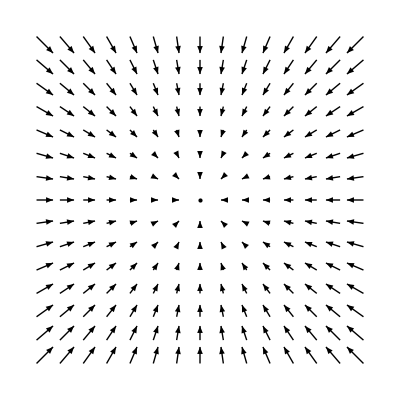

```mathematica
VectorFieldPlot[{-x,-y},{x,-2,2},{y,-2,2}]
```

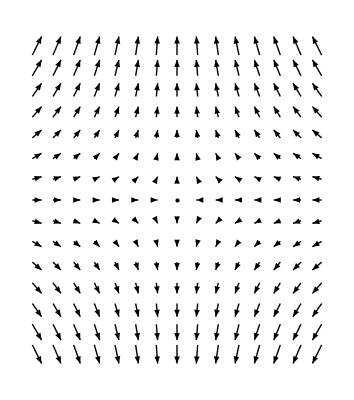

```mathematica
VectorFieldPlot[{-x,2 z},{x,-2,2},{z,-2,2}]
```

```mathematica
Is it from 2 same charge??
```

```mathematica
Ψ[x,y,z]= 1/(√(x^2+y^2+(z-1)^2))+1/(√(x^2+y^2+(z+1)^2))
```

```mathematica
Simplify[Grad[1/(√(Xx^2+Yy^2+(-1+Zz)^2))+1/(√(Xx^2+Yy^2+(1+Zz)^2))]]
```

```mathematica
{-Xx/((Xx^2+Yy^2+(-1+Zz)^2)^(3/2))-Xx/((Xx^2+Yy^2+(1+Zz)^2)^(3/2)),-Yy/((Xx^2+Yy^2+(-1+Zz)^2)^(3/2))-Yy/((Xx^2+Yy^2+(1+Zz)^2)^(3/2)),-(-1+Zz)/((Xx^2+Yy^2+(-1+Zz)^2)^(3/2))-(1+Zz)/((Xx^2+Yy^2+(1+Zz)^2)^(3/2))}/.{Xx->x,Yy->y,Zz->z}
```

{-x/((x^2+y^2+(-1+z)^2)^(3/2))-x/((x^2+y^2+(1+z)^2)^(3/2)),-y/((x^2+y^2+(-1+z)^2)^(3/2))-y/((x^2+y^2+(1+z)^2)^(3/2)),-(-1+z)/((x^2+y^2+(-1+z)^2)^(3/2))-(1+z)/((x^2+y^2+(1+z)^2)^(3/2))}

```mathematica
VectorFieldPlot3D[{-x/((x^2+y^2+(-1+z)^2)^(3/2))-x/((x^2+y^2+(1+z)^2)^(3/2)),-y/((x^2+y^2+(-1+z)^2)^(3/2))-y/((x^2+y^2+(1+z)^2)^(3/2)),-(-1+z)/((x^2+y^2+(-1+z)^2)^(3/2))-(1+z)/((x^2+y^2+(1+z)^2)^(3/2))},{x,-2,2},{z,-2,2},{y,-2,2},VectorHeads->True,ScaleFactor->None,MaxArrowLength->1]
```

-Graphics3D-

```mathematica
{-Xx/((Xx^2+Yy^2+(-1+Zz)^2)^(3/2))-Xx/((Xx^2+Yy^2+(1+Zz)^2)^(3/2)),-Yy/((Xx^2+Yy^2+(-1+Zz)^2)^(3/2))-Yy/((Xx^2+Yy^2+(1+Zz)^2)^(3/2)),-(-1+Zz)/((Xx^2+Yy^2+(-1+Zz)^2)^(3/2))-(1+Zz)/((Xx^2+Yy^2+(1+Zz)^2)^(3/2))}/.{Xx->x,Yy->y,Zz->z}
```

```mathematica
Manipulate[VectorFieldPlot[{-x/((x^2+y^2+(-1+z)^2)^(3/2))-x/((x^2+y^2+(1+z)^2)^(3/2)),-(-1+z)/((x^2+y^2+(-1+z)^2)^(3/2))-(1+z)/((x^2+y^2+(1+z)^2)^(3/2))},{x,-2,2},{z,-2,2}],{y,0.1,2}]
```

```mathematica
*********************************************//(-1+3 Cos[Ttheta]^2)/(2 Rr^3)
```

```mathematica
Grad[(-1+3 Cos[Ttheta]^2)/(2 Rr^3),Spherical]
```

{-(3 (-1+3 Cos[Ttheta]^2))/(2 Rr^4),-(3 Cos[Ttheta] Sin[Ttheta])/Rr^4,0}

```mathematica
Simplify[Laplacian[(-1+3 Cos[Ttheta]^2)/(2 Rr^3),Spherical]]
```

0

```mathematica
Simplify[(-1+3 Cos[Ttheta]^2)/(2 Rr^3)/.{Cos[Ttheta]->Zz/(√(Xx^2+Yy^2+Zz^2)),Sin[Ttheta]->(√(Xx^2+Yy^2))/(√(Xx^2+Yy^2+Zz^2)),Sin[Pphi]->Yy/(√(Xx^2+Yy^2)),Cos[Pphi]->Xx/(√(Xx^2+Yy^2)),Rr->√(Xx^2+Yy^2+Zz^2)}]
```

```mathematica
Simplify[Grad[(-Xx^2-Yy^2+2 Zz^2)/(2 (Xx^2+Yy^2+Zz^2)^(5/2))]]
```

```mathematica
{(3 Xx (Xx^2+Yy^2-4 Zz^2))/(2 (Xx^2+Yy^2+Zz^2)^(7/2)),(3 Yy (Xx^2+Yy^2-4 Zz^2))/(2 (Xx^2+Yy^2+Zz^2)^(7/2)),(3 Zz (3 Xx^2+3 Yy^2-2 Zz^2))/(2 (Xx^2+Yy^2+Zz^2)^(7/2))}/.{Xx->x,Yy->y,Zz->z}
```

```mathematica
VectorFieldPlot3D[{(3 x (x^2+y^2-4 z^2))/(2 (x^2+y^2+z^2)^(7/2)),(3 y (x^2+y^2-4 z^2))/(2 (x^2+y^2+z^2)^(7/2)),(3 z (3 x^2+3 y^2-2 z^2))/(2 (x^2+y^2+z^2)^(7/2))},{x,-2,2},{z,-2,2},{y,-2,2},VectorHeads->True,ScaleFactor->None,MaxArrowLength->1]
```

Power::infy: Infinite expression 1/0 encountered.

∞::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

∞::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power :: "infy" will be suppressed during this calculation.

∞::indet: Indeterminate expression 0\ ComplexInfinity encountered.

General::stop: Further output of ∞ :: "indet" will be suppressed during this calculation.

-Graphics3D-

```mathematica
Manipulate[VectorFieldPlot[{(3 x (x^2+y^2-4 z^2))/(2 (x^2+y^2+z^2)^(7/2)),(3 z (3 x^2+3 y^2-2 z^2))/(2 (x^2+y^2+z^2)^(7/2))},{x,-2,2},{z,-2,2}],{y,-2,2}]
```